# Project Euler Problem 30

As a first step, define a function to calculate the sum of pth powers of digits:

```mathematica
digitPowerSum[n_,p_]:=Total[IntegerDigits[n]^p]
```

```mathematica
digitPowerSum[1634,4]
```

1634

At first glance it isn’t obvious why there can’t be infinitely many cases. Plotting gives us some insight:

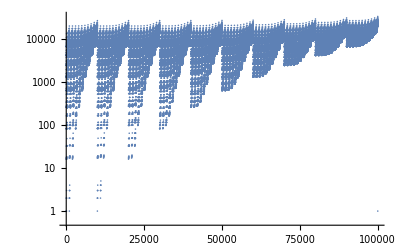

```mathematica
ListLogPlot[Table[{n,digitPowerSum[n,4]},{n,100000}],PlotRange->All]
```

The maximum possible digit power sum for a k digit number is k 9^p, which increases linearly with k. Meanwhile, the smallest number with k digits is 10^(k-1), which increases exponentially with k. There will therefore be a value of k for which all digit sums are less than all numbers. This k value can serve as an upper bound for our search.

```mathematica
maxDigitsForPower[p_]:=Module[{k=1},While[k 9^p≥10^(k-1),k+=1];k-1]
```

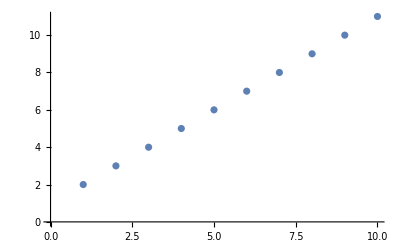

```mathematica
ListPlot[Table[{p,maxDigitsForPower[p]},{p,Range[10]}]]
```

Putting the above pieces together we can now search for all numbers equal to their own power digit sum:

```mathematica
digitPowerSumSolutions[p_]:=Select[Range[10,10^maxDigitsForPower[p]],#==digitPowerSum[#,p]&]
```

```mathematica
digitPowerSumSolutions[4]
```

{1634,8208,9474}

```mathematica
digitPowerSumSolutions[5]
```

{4150,4151,54748,92727,93084,194979}

```mathematica
solution[p_]:=Total[digitPowerSumSolutions[p]]
```

```mathematica
solution[4]
```

19316

```mathematica
solution[5]
```

443839